Which characters should appear in the pullback?
Before we take the pullback it would be nice to reduce the characters that would appear in the Coset CFT character expansion in TIsing^2 characters.

```mathematica
p=5;
p'=4;
cv=1-6(p-p')^2/(p p');
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
hvf[i_,j_]:=hv@@i+hv@@j;
H={{1,1},{1,2},{1,3},{1,4},{2,2},{2,4}};

Hf=Tuples[H,2];
ηinv[q_,N_:∞]:=∑_(k=0)^N PartitionsP[k] q^k;
χv[r_,s_,q_,N_:∞]:=Series[ηinv[q] q^(p/(4 p')+p'/(4 p)-41/80)∑_(n=-N)^N (q^(n^2 p p'+n (p r-s p'))-q^(n^2 p p'+n (p r+s p')+r s)),{q,0,N}];
χvf[i_,j_,q_,N_]:=χv[i[[1]],i[[2]],q,N]χv[j[[1]],j[[2]],q,N];
```

```mathematica
k=8;
cw=(2(k-1))/(k+2);
hw[l_,m_]:=(l(l+2))/(4(k+2))-m^2/(4k);
χw[l_,m_,q_,N_:∞]:=Series[ηinv[q]^2∑_(r=0)^N ∑_(s=0)^N (-1)^(r+s)(q^(1/2 (r^2+s (1+l-m+s)+r (1+l+m+18 s)))-q^(1/2 (18+r^2+s (19+m+s)-l (2+r+s)+r (19-m+18 s)))),{q,0,N}];
χM[A_,q_,χ:χvf,N_:∞]:=χ[A[[1,1]],A[[1,2]],q,N]χ[A[[2,1]],A[[2,2]],q,N];
(*This is the super ugly way to calculate which are the possible values l,m without degeneracies*)
w=ConstantArray[0,{k+1,2k+1}];
M[m_]:=m+k+1;
L[l_]:=l+1
For[l=0,l<=k,l++,For[m=-l,m<=l,m=m+2,If[w[[L[l],M[m]]]==0,w[[L[l],M[m]]]=1;If[0<M[k-m]<=2k+1,w[[L[k-l],M[k-m]]]=-1];If[0<M[k+m]<=2k+1,w[[L[k-l],M[k+m]]]=-1];]]]
W={#[[1]]-1,#[[2]]-k-1}&/@Position[w,_?(# ==1&),{2}];
```

The conformal weights of the two models

TIsing^2

```mathematica
Sort[hvf @@@Hf]
```

{0,3/80,3/80,3/40,1/10,1/10,11/80,11/80,1/5,7/16,7/16,19/40,19/40,43/80,43/80,3/5,3/5,51/80,51/80,7/10,7/10,7/8,83/80,83/80,6/5,3/2,3/2,123/80,123/80,8/5,8/5,31/16,31/16,21/10,21/10,3}

Coset

```mathematica
Sort[hw @@@W]
```

{0,7/160,7/160,3/40,3/40,3/32,3/32,1/10,1/5,11/32,11/32,19/40,19/40,19/32,19/32,3/5,7/10,7/10,127/160,127/160,27/32,27/32,7/8,7/8,43/40,43/40,6/5,207/160,207/160,3/2,3/2,247/160,247/160,15/8,15/8,2}

Now let’s find the compatible combinations of characters

```mathematica
Wpairs=Tuples[W,2];
Hfpairs=Tuples[Hf,2];
weightsM=Sort[DeleteDuplicates[(hw@@#1+hw@@#2)&@@@Wpairs]];
allowedModules=Function[h,{h,Hfpairs[[Position[Hfpairs,_?(((hvf@@#1+hvf@@#2)&@@# - h)∈Integers&),1]//Flatten]]}]/@weightsM;
weightsToModules=Function[h,{h,Wpairs[[Position[Wpairs,_?((hw@@#1+hw@@#2)&@@# == h&),1]//Flatten]]}]/@weightsM;
```

```mathematica
n=6;
i=3;
h=allowedModules[[i,1]];
cpf=DeleteDuplicates[χM[#,q,χw,n]&/@weightsToModules[[i,2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#1+hvf@@#2)&@@#-h)χM[#,q,χvf,n]&/@allowedModules[[i,2]]];
Coefficients[targetPf_,pfs_]:=LinearSolve[Transpose[CoefficientList[#,q,n]&@pfs],CoefficientList[targetPf,q,n]];
x=Coefficients[cpf,pfs]
Total[x*pfs]-cpf
```

{1,-1,0,-4,4,1}

3 q^6+O[q]^7

```mathematica
weightsC=Sort[DeleteDuplicates[hw@@@W]];
allowedCharacters=Function[h,{h,Hf[[Position[Hf,_?((hvf@@# - h)∈Integers&),1]//Flatten]]}]/@weightsC;
weightsToCharacters=Function[h,{h,W[[Position[W,_?(hw@@# == h&),1]//Flatten]]}]/@weightsC;
```

```mathematica
n=10;
i=5;
h=allowedCharacters[[i,1]];
cpf=DeleteDuplicates[χw[#[[1]],#[[2]],q,n]&/@weightsToCharacters[[i,2]]][[1]];
pfs= DeleteDuplicates[q^((hvf@@#)&@#-h)χvf[#[[1]],#[[2]],q,n]&/@allowedCharacters[[i,2]]];
x=LinearSolve[Transpose[CoefficientList[#,q,n]&@pfs],CoefficientList[cpf,q,n]]
Total[x*pfs]-cpf
```

{1,1}

O[q]^11

The Modular S matrix of the Coset Model
In our effort to find the Cardy states in the gauged theory we want to calculate the S matrix and express the Cardy states as linear combinations of the Ishibashi states in the coset model using coefficients from the S-matrix. The matrix is given by

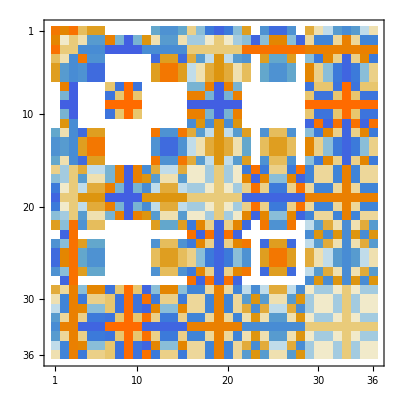

```mathematica
S=Array[(1/(√(2(k+2)))Sin[(π(W[[#1,1]]+1)(W[[#2,1]]+1))/(k+2)] ⅇ^(-ⅈ π (W[[#1,2]]W[[#2,2]])/(k+2)))&,{Length[W],Length[W]}]//Simplify;
S//MatrixPlot
```